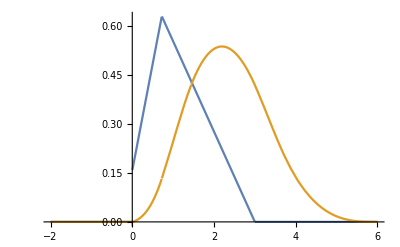

1.

1.

1.34598

3.18747

```mathematica
f0[x_]:=If[0<=x<0.1,10,0.0];
x1=0.7226;
x2=3.0; 
y1=0.1;
y2=0.4;f1[x_]:=If[0<=x<x1,((y2-y1) x)/x1+y1,If[x1<=x<x2,((0-y2) (x-x1))/(x2-x1)+y2,0]]/0.63613;
f2[x_]:=Integrate[f1[x-i2] f1[i2],{i2,0,2*x2}];
f2[x_]:=Piecewise[{{-8.442973240360974*^-6 (-85839.+25000. x), x==1.4452}, {-0.017101605524720797 (-216.+108. x-18. x^2+x^3), 3.7226≤x<6.}, {2.5480671079975306*^-9 (1.3053769*^7 x+5.4195*^7 x^2+3.75*^7 x^3), 0.<x<0.7226}, {-2.0384536863980247*^-12 (4.7163267397*^10-2.284409575*^11 x+6.774375*^10 x^2+4.6875*^10 x^3), x==0.7226}, {6.840642209888319*^-14 (-8.538327477397*^12+1.6134581535*^13 x-4.5*^12 x^2+2.5*^11 x^3), 1.4452<x<3.}, {-4.4753966944718203*^-13 (2.42969802397*^11 x-1.1867530775*^12 x^2+3.9415625*^11 x^3), 0.7226<x<1.4452}, {1.893341325737149*^-17 (-7.461049921333536*^16+1.06684153610955*^17 x-3.39312663375*^16 x^2+3.0383125*^15 x^3), x==3.}, {1.893341325737149*^-17 (-1.1837202125083536*^17+1.55074064135955*^17 x-5.1604032675*^16 x^2+5.173375*^15 x^3), 3.<x<3.7226}, {0., True}}]
Plot[{f1[x],f2[x]},{x,-2,6}]
Integrate[f1[x],{x,0,3}]
Integrate[f1[x],{x,0,3}]
Integrate[f2[x],{x,0,6}]
Integrate[x f2[x],{x,0,6}]

PoisD[μ_,n_]:=(ⅇ^-μ μ^n)/(n!);
PoisDx[μ_,x_]:=(ⅇ^-μ μ^x)/Gamma[x+1];
F[i_][x_]:=ToExpression["f"<>ToString[i]][x];
sumP[μ_,x_,m_]:=∑_(i=0)^m PoisD[μ,i]F[i][x];
```

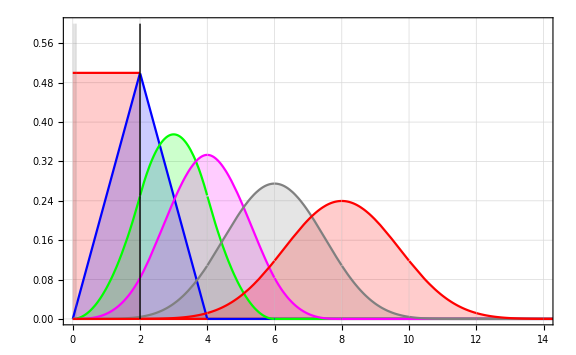

```mathematica
lineStyle={Thick,Black};
line1=Line[{{2.,0},{2.,0.6}}];

Plot[{f0[x],f1[x],f2[x],f3[x],f4[x],f6[x],f8[x]},{x,0,16},
PlotRange->{{0,14},{0,0.6}},
Frame->True,
Filling->Axis,
PlotStyle->{Gray,Red,Blue,Green,Magenta},
ImageSize->Large,BaseStyle->{FontSize->16},
GridLines->Automatic,
Epilog->{Directive[lineStyle],line1}
]
```

k =4.

Integral sumP = 0.978637

NIntegrate[x*sumP[k,x]=3.79638

Sqrt[NIntegrate[x^2*sumP[k,x] =4.39203

Integral PoisD[k,x] = 0.993828

NIntegrate[x*PoisDx[k,x] =4.00131

Sqrt[NIntegrate[x^2*PoisDx[k,x]] =4.47202

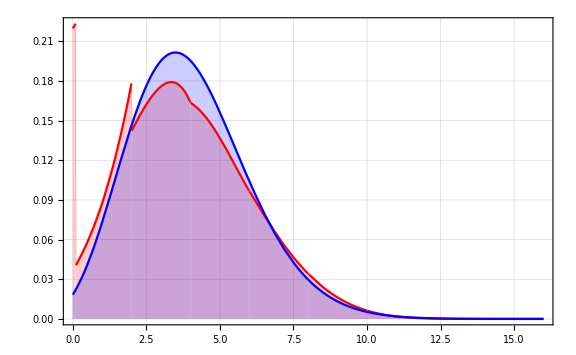

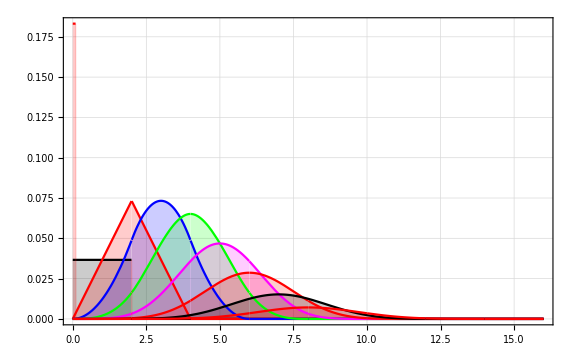

```mathematica
k=4.0;
sumP[μ_,x_]:=PoisD[μ,0] f0[x]+PoisD[μ,1] f1[x]+PoisD[μ,2] f2[x]+PoisD[μ,3] f3[x]+PoisD[μ,4] f4[x]+PoisD[μ,5] f5[x]+PoisD[μ,6] f6[x]+PoisD[μ,7] f7[x]+PoisD[μ,8] f8[x];
Print["k =",k]
Print["Integral sumP = ",Integrate[sumP[k,x],{x,0,16}]]
Print["NIntegrate[x*sumP[k,x]=", NIntegrate[x*sumP[k,x],{x,0,16}]]
Print["Sqrt[NIntegrate[x^2*sumP[k,x] =",Sqrt[NIntegrate[x^2*sumP[k,x],{x,0,16}]]]
Print["Integral PoisD[k,x] = ",NIntegrate[PoisDx[k,x],{x,0,16}]]
Print["NIntegrate[x*PoisDx[k,x] =",NIntegrate[x*PoisDx[k,x],{x,0,16}]]
Print["Sqrt[NIntegrate[x^2*PoisDx[k,x]] =",Sqrt[NIntegrate[x^2*PoisDx[k,x],{x,0,16}]]]
μ=4.0; n=8;
Plot[{sumP[μ,x,n],PoisDx[4,x],},{x,0,16},
PlotRange->{{0,16},{0,All}},
Frame->True,
Filling->Axis,
PlotStyle->{Red,Blue,Green,Magenta},
ImageSize->Large,BaseStyle->{FontSize->16},
GridLines->Automatic
]
Plot[{PoisD[k,0] f0[x],PoisD[k,1] f1[x],PoisD[k,2] f2[x],PoisD[k,3] f3[x],PoisD[k,4] f4[x],PoisD[k,5] f5[x],PoisD[k,6] f6[x],PoisD[k,7] f7[x],PoisD[k,8] f8[x]},{x,0,16},
PlotRange->{{0,16},{0,All}},
Frame->True,
Filling->Axis,
PlotStyle->{Red,Black,Red,Blue,Green,Magenta},
ImageSize->Large,BaseStyle->{FontSize->16},
GridLines->Automatic
]
Integrate[f8[x],{x,0,16}]
PoisD[4,1]
PoisD[4,2]
```